```mathematica
Inverse average tax
```

```mathematica
Clear["`*"];
$Assumptions=True;
T2=Wi (c0+c1 (1-(1-ⅇ^(-Wi gamma))/(gamma Wi)))
Solve[T2==T,Wi]
```

(c0+c1 (1-(1-ⅇ^(-gamma Wi))/(gamma Wi))) Wi

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{Wi→(c1+gamma T+c0 ProductLog[-(c1 ⅇ^((gamma (-c1/gamma-T))/(c0+c1)))/(c0+c1)]+c1 ProductLog[-(c1 ⅇ^((gamma (-c1/gamma-T))/(c0+c1)))/(c0+c1)])/((c0+c1) gamma)}}

#### dWdF

```mathematica
Clear["`*"];
$Assumptions=True;
$Assumptions={Wtilda0> 0, sigma>0, mu∈Reals, c0>0, c1≥0, gamma≥0,tau≥ 0, F>0, Wi>0, rho>0};
T2=Wi (c0+c1 (1-(1-ⅇ^(-Wi gamma))/(gamma Wi)));
Xi=Wi-T2;
EUA0fun=Log[Xi];
EUAWCfun=rho*Log[Xi-F]+(1-rho)*Log[Wi-F];
DeltaW0=EUAWCfun-EUA0fun;
Print["dDeltaW0dWfun"]
dDeltaW0dWfun = FullSimplify[D[DeltaW0, Wi]]
Print["dDeltaW0dWfun c1 = 0"]
FullSimplify[dDeltaW0dWfun/.c1->0]
Print["dDeltaW0dFfun"]
dDeltaW0dFfun=FullSimplify[-(rho/(Xi-F)+(1-rho)/(Wi-F))]
Print["dWdF"]
dWdF=FullSimplify[-dDeltaW0dFfun/dDeltaW0dWfun]
```

dDeltaW0dWfun

(-1+rho)/(F-Wi)+((c1-(-1+c0+c1) ⅇ^(gamma Wi)) gamma)/(c1+ⅇ^(gamma Wi) (-c1+(-1+c0+c1) gamma Wi))+((-c1+(-1+c0+c1) ⅇ^(gamma Wi)) gamma rho)/(c1+ⅇ^(gamma Wi) (-c1+F gamma+(-1+c0+c1) gamma Wi))

dDeltaW0dWfun c1 = 0

(F (-F+Wi+c0 (-1+rho) Wi))/((F-Wi) Wi (F+(-1+c0) Wi))

dDeltaW0dFfun

(-1+rho)/(-F+Wi)+(ⅇ^(gamma Wi) gamma rho)/(c1+ⅇ^(gamma Wi) (-c1+F gamma+(-1+c0+c1) gamma Wi))

dWdF

-((-1+rho)/(-F+Wi)+(ⅇ^(gamma Wi) gamma rho)/(c1+ⅇ^(gamma Wi) (-c1+F gamma+(-1+c0+c1) gamma Wi)))/((-1+rho)/(F-Wi)+((c1-(-1+c0+c1) ⅇ^(gamma Wi)) gamma)/(c1+ⅇ^(gamma Wi) (-c1+(-1+c0+c1) gamma Wi))+((-c1+(-1+c0+c1) ⅇ^(gamma Wi)) gamma rho)/(c1+ⅇ^(gamma Wi) (-c1+F gamma+(-1+c0+c1) gamma Wi)))

#### Optimal Avoidance out of equilibrium

```mathematica
Clear["`*"];
$Assumptions=True;
$Assumptions={1>t1>0, 1>p>0, t>0,w0>0, w0-t1 w0>0,w0-tau>0, w0-t1 w0-tau>0}
T[w_]:=t1 w;x[w_]:=w-T[w];ws[f_,w_]:=x[w]-f;wup[f_,w_,A_]:=x[w]+ A-f;
U[z_]:=Log[z];
avoid[w_]:=((1-p-rho)/(p (1-p))) x[w]
zpp[w_]:=U[x[w]]-rho U[ws[tau,w]]-(1-rho) U[wup[tau,w,T[w]]]
int[d1_,d2_]:=(d1-d2)/20;
p+rho≤1
((1-p-rho)/(p (1-p))) ((1-T'[w])/T'[w])<1
Print["Curly A"]
curlyA=((1-p-rho)/(p (1-p))) (1-T'[w])
Print["tau/p"]
tau/p
FullSimplify[Solve[zpp[w0]==0,w0]]
FullSimplify[Solve[T[w1]==tau/p,w1]]
FullSimplify[Solve[p avoid[w2]-tau==0,w2]]
```

{1>t1>0,1>p>0,t>0,w0>0,w0-t1 w0>0,-tau+w0>0,-tau+w0-t1 w0>0}

p+rho≤1

((1-p-rho) (1-t1))/((1-p) p t1)<1

Curly A

((1-p-rho) (1-t1))/((1-p) p)

tau/p

tau/p

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[(-1+rho) Log[-tau+w0]+Log[w0-t1 w0]==rho Log[-tau+w0-t1 w0],w0]

{{w1→tau/(p t1)}}

{{w2→-((-1+p) tau)/((-1+p+rho) (-1+t1))}}

```mathematica
Avoidance and Revenues
```

and Avoidance Revenues

```mathematica
Clear["`*"];
$Assumptions=True;
$Assumptions={W0> 0, sigma>0, mu∈Reals, c0>0, c1≥0, gamma≥0}
T2=Wi (c0+c1 (1-(1-ⅇ^(-Wi gamma))/(gamma Wi)))
mu = 10.2548;
sigma=0.60909;
c1=0;
Print["Avoidance"]
A2 =FullSimplify[Integrate[T2 PDF[LogNormalDistribution[mu,sigma],Wi], {Wi,W0,Infinity}]]
Print["Expected Revenues from avoidance enforcement"]
RA2 =rho*A2
Print["Revenues from compliance"]
RC2=FullSimplify[Integrate[T2 PDF[LogNormalDistribution[mu,sigma],Wi], {Wi,0,W0}]]
Print["Total revenues"]
R2 =FullSimplify[FullSimplify[Integrate[T2 PDF[LogNormalDistribution[mu,sigma],Wi], {Wi,0,W0}]]+ RA2]

(*FullSimplify[t ∫_0^w0pp[t] w g[w]ⅆw + rho t ∫_w0pp[t]^∞ w g[w]ⅆw]*)
```

{W0>0,sigma>0,mu∈ℝ,c0>0,c1≥0,gamma≥0}

(c0+c1 (1-(1-ⅇ^(-gamma Wi))/(gamma Wi))) Wi

Avoidance

17105.4 c0 (1.+Erf[12.3357-1.16092 Log[W0]])

Expected Revenues from avoidance enforcement

17105.4 c0 rho (1.+Erf[12.3357-1.16092 Log[W0]])

Revenues from compliance

17105.4 c0 Erfc[12.3357-1.16092 Log[W0]]

Total revenues

17105.4 c0 rho (1.+Erf[12.3357-1.16092 Log[W0]])+17105.4 c0 Erfc[12.3357-1.16092 Log[W0]]

### Total avoidance and revenues exported to R

```mathematica
(*A_lin_fun = 17105.3769312732 c0 (1.+Erf[12.33572806744155-1.1609233137739046 Log[W0]])
RA_lin_fun = 17105.3769312732 c0 rho (1.+Erf[12.33572806744155-1.1609233137739046 Log[W0]])
RC_lin_fun = 17105.3769312732 c0 Erfc[12.33572806744155-1.1609233137739046 Log[W0]]
R_lin_fun = 17105.3769312732 c0 rho (1.+Erf[12.33572806744155-1.1609233137739046 Log[W0]])+17105.3769312732 c0 Erfc[12.33572806744155-1.1609233137739046 Log[W0]]*)
```

#### Tax schedules

Parameters to match UK tax schedule

Marginal tax

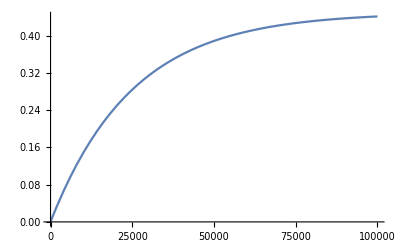

Average tax

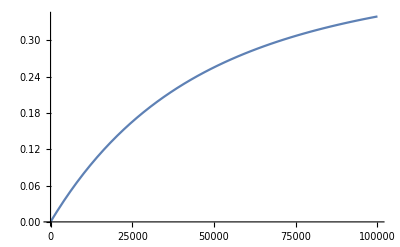

1/2 (-(2 c10 ⅇ^(-gamma W))/gamma^2+c00 W^2+c10 W (-2/gamma+W))

(c01 W^2)/2

```mathematica
Clear["`*"];
$Assumptions=True;
Print["Parameters to match UK tax schedule"]
c0=0.0;c1=0.45;gamma =.00004;
Print["Marginal tax"]
Plot[c0+c1 (1-Exp[-gamma W]),{W,0,100000}]
Print["Average tax"]
Plot[c0+c1 (1-(1-ⅇ^(-W gamma))/(gamma W)),{W,0,100000}]
Clear[c00,c10,c01,gamma]
∫(c00+c10 (1-(1-ⅇ^(-W gamma))/(gamma W))) WⅆW
∫(c01 W)ⅆW
```

#### Minimum W s.t. W^u is positive

```mathematica
Clear["`*"];
$Assumptions=True;
$Assumptions={W0> 0, sigma>0, mu∈Reals, c0>0, c1≥0, gamma≥0,tau>0,F_>0}
T2=Wi (c0+c1 (1-(1-ⅇ^(-Wi gamma))/(gamma Wi)))
Xi=Wi-T2
FullSimplify[Solve[FullSimplify[Xi-F]==0, Wi]]
(*Wmin_analyt_fun=(c1-F gamma+(-1+c0+c1) ProductLog[-(c1 ⅇ^((-c1+F gamma)/(-1+c0+c1)))/(-1+c0+c1)])/((-1+c0+c1) gamma)*)
```

{W0>0,sigma>0,mu∈ℝ,c0>0,c1≥0,gamma≥0,tau>0,F_>0}

(c0+c1 (1-(1-ⅇ^(-gamma Wi))/(gamma Wi))) Wi

Wi-(c0+c1 (1-(1-ⅇ^(-gamma Wi))/(gamma Wi))) Wi

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{Wi→(c1-F gamma+(-1+c0+c1) ProductLog[-(c1 ⅇ^((-c1+F gamma)/(-1+c0+c1)))/(-1+c0+c1)])/((-1+c0+c1) gamma)}}